```mathematica
(*This file contains attempts to improve the heuristic of HWS*)
(*Input is a CSV with columns defined below, they can be computed using aws_vs_ws_experiment.R*)
```

```mathematica
data=Import[filename,"Table","FieldSeparators"->" "];
data[[1]]=Join[{"id"},data[[1]]];(*Note that id header is missing in csv*)
data=Join[{data[[1]]},Select[data,#[[2]]/#[[3]]>10&]];(*Remove data with small n compared to k*)
kfactors=data[[2;;,-1]];
data[[1,-1]]
epsilons=data[[2;;,-3]];
data[[1,-3]]
skews=data[[2;;,-9]];
data[[1,-9]]
ratios=data[[2;;,6]];
data[[1,6]]
```

k_factor

epsilon0.95

skew

max_weight_ratio

```mathematica
NonlinearModelFit[Transpose[{kfactors,epsilons}],a*x^-1,{a},x]//Normal
```

0.00232666/x

```mathematica
((-1+ratio)^2 skew^2)/(ratio^2 (1+skew)^2 (1+2 skew))
```

```mathematica
(data[[1,3]]*data[[1,6]]^2(1+data[[1,-9]])^2(1+2data[[1,-9]]))/(data[[1,4]]^2*(data[[1,6]]-1)^2*data[[1,-9]]^2)
```

(k max_weight_ratio^2 (1+skew)^2 (1+2 skew))/(m^2 (-1+max_weight_ratio)^2 skew^2)

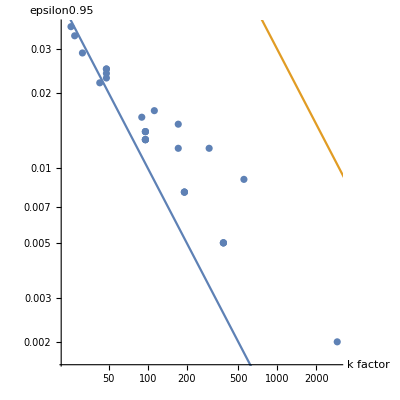

```mathematica
Show[ListLogLogPlot[Transpose[{(data[[2;;,3]]*data[[2;;,6]]^2(1+data[[2;;,-9]])^2(1+2data[[2;;,-9]]))/(data[[2;;,4]]^2*(data[[2;;,6]]-1)^2*data[[2;;,-9]]^2),epsilons}],AspectRatio->1,PlotRange->Full,AxesLabel->{"k factor","epsilon0.95"}],LogLogPlot[{1 x^-1,30 x^-1},{x,0.0001,10^9}]]
```

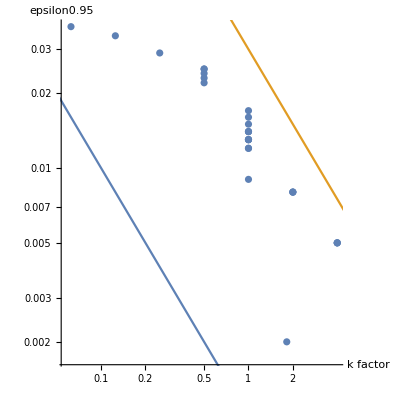

```mathematica
Show[ListLogLogPlot[Transpose[{kfactors,epsilons}],AspectRatio->1,PlotRange->Full,AxesLabel->{"k factor","epsilon0.95"}],LogLogPlot[{0.001 x^-1,0.03 x^-1},{x,0.0001,10}]]
```

Note that the "badness" could be defined as the line the data lies on, ie α s.t. the data is on α x^-1.

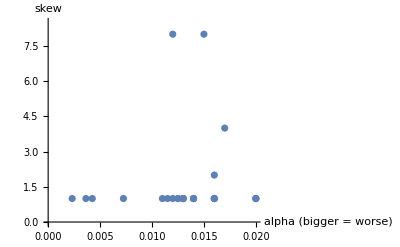

```mathematica
ListPlot[Transpose[{epsilons*kfactors,skews}],AxesLabel->{"alpha (bigger = worse)","skew"}]
```

```mathematica
(*Obtain the 10 worst alphas*)
worst10alphas=(Transpose[{epsilons*kfactors,Table[i,{i,1,Length[epsilons]}]}]//Sort)[[-10;;-1]][[All,2]]
```

{381,388,312,326,340,342,365,389,390,366}

```mathematica
best10alphas=(Transpose[{epsilons*kfactors,Table[i,{i,1,Length[epsilons]}]}]//Sort)[[1;;10]][[All,2]]
```

{167,247,85,89,93,133,137,141,213,217}

```mathematica
biggest10n=(Transpose[{data[[2;;,2]],Table[i,{i,1,Length[epsilons]}]}]//Sort)[[-10;;-1]][[All,2]]
```

{311,312,313,314,364,365,366,352,354,351}

```mathematica
Join[{data[[1]]},Table[data[[i]],{i,worst10alphas}]]//Transpose//TableForm
```

id | 576 | 583 | 480 | 494 | 508 | 510 | 542 | 593 | 594 | 543
n | 4800000 | 600000. | 12800000 | 3200000 | 6400000 | 6400000 | 19200000 | 9600000 | 9600000 | 19200000
k | 160000 | 20000 | 640000 | 160000 | 320000 | 320000 | 640000 | 320000 | 320000 | 640000
m | 100 | 100 | 100 | 100 | 100 | 100 | 100 | 100 | 100 | 100
skew | 8 | 8 | 2 | 4 | 1 | 2 | 1 | 1 | 4 | 4
max_weight_ratio | 2 | 4 | 32 | 8 | 16 | 16 | 8 | 4 | 4 | 8
n_outer | 1000 | 1000 | 1000 | 1000 | 1000 | 1000 | 1000 | 1000 | 1000 | 1000
n_inner | 1000 | 1000 | 1000 | 1000 | 1000 | 1000 | 1000 | 1000 | 1000 | 1000
n_cores | 4 | 4 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4
epsilon0.9 | 0.003 | 0.035 | 0.005 | 0.012 | 0.005 | 0.007 | 0.003 | 0.003 | 0.005 | 0.005
epsilon0.95 | 0.003 | 0.042 | 0.006 | 0.014 | 0.006 | 0.008 | 0.003 | 0.004 | 0.006 | 0.006
epsilon0.99 | 0.004 | 0.052 | 0.008 | 0.017 | 0.008 | 0.01 | 0.004 | 0.005 | 0.008 | 0.008
k_factor | 8 | 0.5 | 2 | 2 | 2 | 2 | 8 | 8 | 8 | 8

```mathematica
Join[{data[[1]]},Table[data[[i]],{i,best10alphas}]]//Transpose//TableForm
```

id | 232 | 344 | 102 | 106 | 110 | 198 | 202 | 206 | 294 | 298
n | 400000. | 40000 | 1.×10^6 | 1.×10^6 | 1.×10^6 | 100000. | 100000. | 100000. | 400000. | 400000.
k | 10000 | 1600 | 400 | 400 | 400 | 400 | 400 | 400 | 400 | 400
m | 100 | 100 | 100 | 100 | 100 | 100 | 100 | 100 | 100 | 100
skew | 16 | 16 | 16 | 32 | 4 | 16 | 32 | 4 | 16 | 32
max_weight_ratio | 4 | 4 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16
n_outer | 1000 | 1000 | 1000 | 1000 | 1000 | 1000 | 1000 | 1000 | 1000 | 1000
n_inner | 1000 | 1000 | 1000 | 1000 | 1000 | 1000 | 1000 | 1000 | 1000 | 1000
n_cores | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
epsilon0.9 | 0.065 | 0.364 | 1 | 1 | 0.999 | 1 | 1 | 0.999 | 1 | 1
epsilon0.95 | 0.075 | 0.451 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
epsilon0.99 | 0.098 | 0.569 | 1 | 1.452 | 2.541 | 1 | 1 | 2.293 | 1 | 1
k_factor | 0.25 | 0.04 | 0.0025 | 0.0025 | 0.0025 | 0.0025 | 0.0025 | 0.0025 | 0.0025 | 0.0025

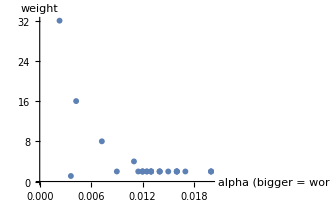

```mathematica
ListPlot[Transpose[{epsilons*kfactors,ratios}],AxesLabel->{"alpha (bigger = worse)","weight"}]
```

```mathematica
ListPointPlot3D[Transpose[{Log[epsilons*kfactors+0.001],Log[ratios],Log[skews]}],AxesLabel->{"alpha (bigger = worse)","ratio","skew"},BoxRatios->{1,1,1},ImageSize->500]
```

-Graphics3D-

```mathematica
(ratios//Tally//Sort)[[All,1]]
```

{1.1,1.5,2,4,8,16,32}

```mathematica
(skews//Tally//Sort)[[All,1]]
```

{1,2,4,8,16,32}

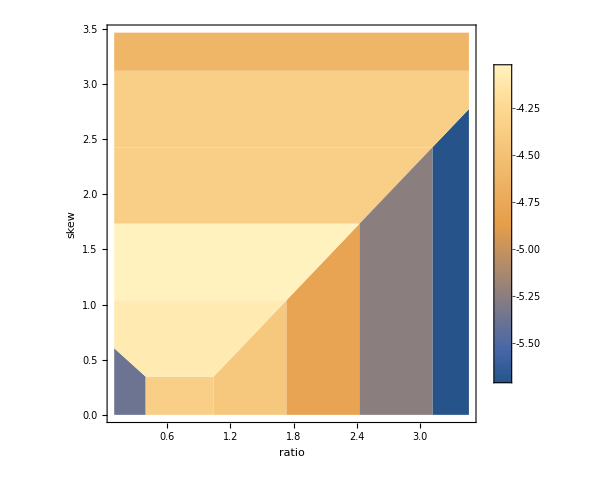

```mathematica
ListDensityPlot[Transpose[{Log[ratios],Log[skews],Log[epsilons*kfactors+0.001]}],FrameLabel->{"ratio","skew"},ImageSize->500,InterpolationOrder->0,PlotLegends->Automatic]
```

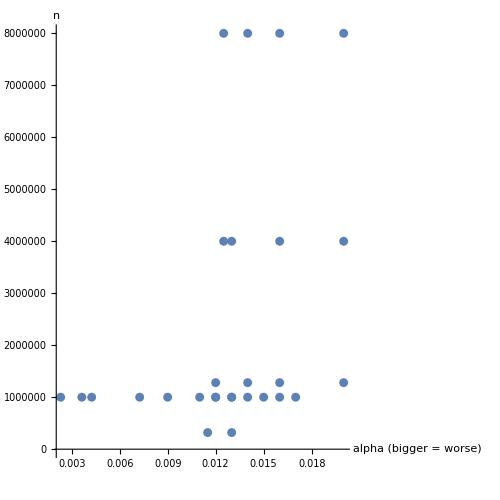
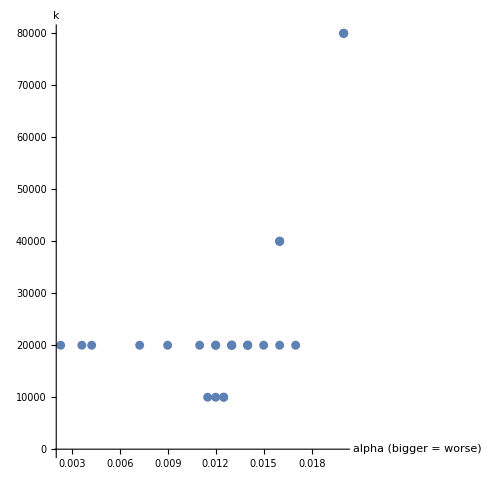
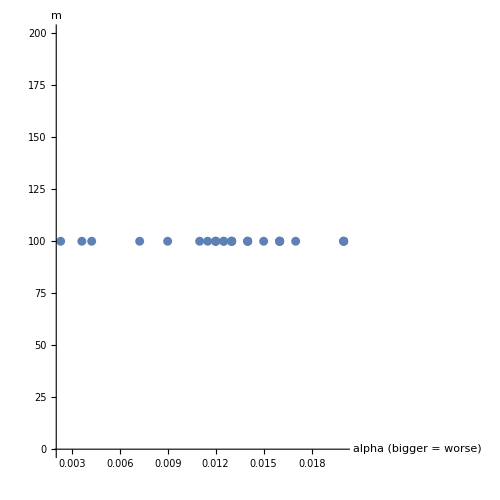
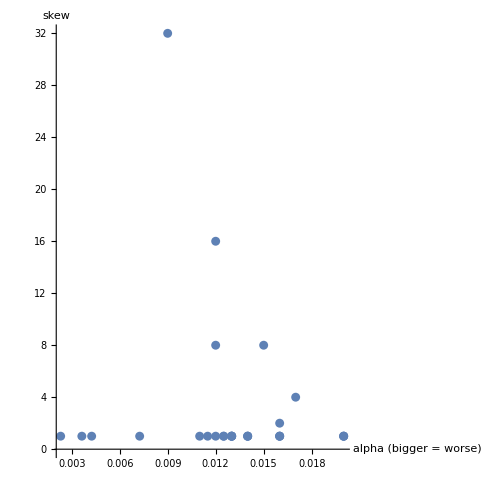
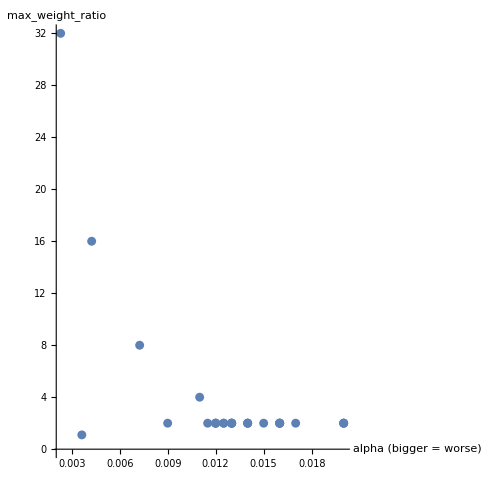
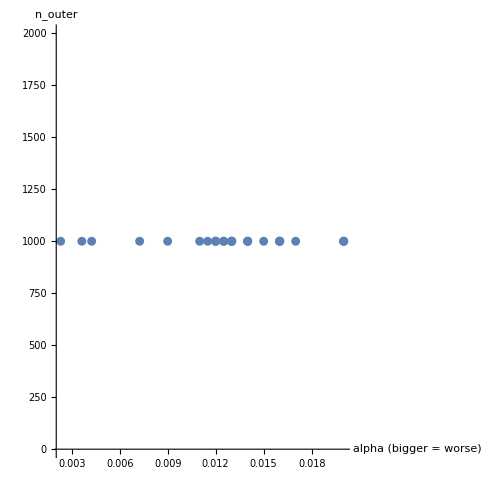
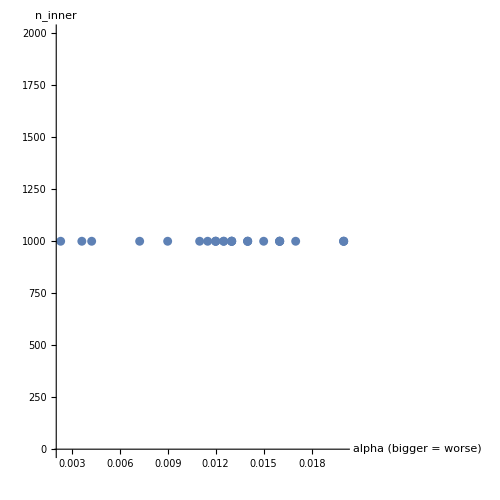
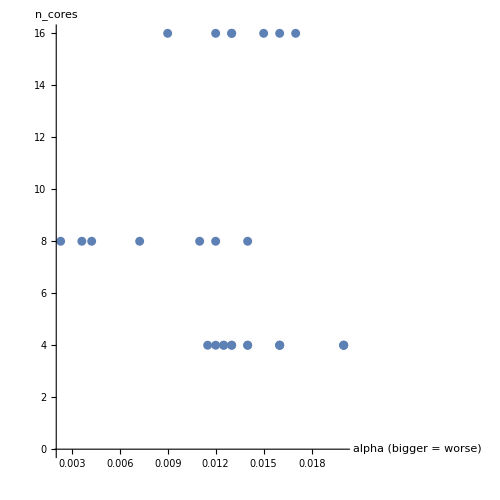

```mathematica
Table[
ListPlot[Transpose[{epsilons*kfactors,data[[2;;,i]]}],AxesLabel->{"alpha (bigger = worse)",data[[1]][[i]]},ImageSize->500,PlotRange->Full,AspectRatio->1]
,{i,2,Length[data[[1]]]}]
```

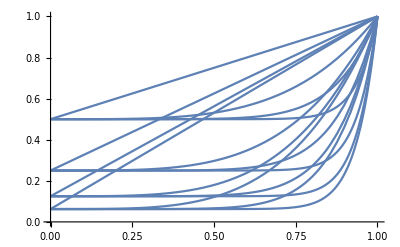

```mathematica
Table[Plot[(x^skew*(ratio-1)+1)/((ratio-1)+1),{x,0,1},PlotRange->{Full,{0,1}}],{skew,{1,4,8,16}},{ratio,{16,8,2,4}}]//Show
```

```mathematica
Integrate[(x^skew*(ratio-1)+1)/((ratio-1)+1),{x,0,1}]
```

ConditionalExpression[(ratio+skew)/(ratio+ratio skew),Re[skew]>-1]

```mathematica
mean=(ratio+skew)/(ratio+ratio * skew);
```

```mathematica
Integrate[((x^skew*(ratio-1)+1)/((ratio-1)+1)-mean)^2,{x,0,1}]
```

ConditionalExpression[((-1+ratio)^2 skew^2)/(ratio^2 (1+skew)^2 (1+2 skew)),Re[skew]>-1/2]

```mathematica
sqError=((-1+ratio)^2 skew^2)/(ratio^2 (1+skew)^2 (1+2 skew));
```